### Simplex Plot

```mathematica
triangle=Graphics[{Thickness[0.005],Darker[Gray],Line[{{0,0},{1,0},{1/2,(√3)/2},{0,0}}]}];
```

```mathematica
(*Define the triangle vertices in 2D*)
v1={1,0}; (*corresponds to {1,0,0}*)
v2={0,0}; (*corresponds to {0,1,0}*)
v3={1/2,Sqrt[3]/2}; (*corresponds to {0,0,1}*)

(*Barycentric to Cartesian conversion function*)
barycentricToCartesian[{x1_,x2_,x3_}]:=x1*v1+x2*v2+x3*v3
```

## Core parameters

```mathematica
α=0.8;β=2;γ=.;u=0;
q1=2;q2=2.5;q3=3;
p[γ_,y_,q_]:=(1-γ)q/(q1+q2+q3)+α γ (y^β/(y^β+(1-y)^β));
```

```mathematica
cols=ColorData[97,"ColorList"]⟦{2,1,3}⟧
```

{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885]}

## Trajectory

```mathematica
plotlist={};
initialconditions={};
Table[If[x>0&&x<1&&y>0&&y<1&&x+y<1,AppendTo[initialconditions,{x,y,1-x-y}]],{x,0,1,0.05},{y,0,1,0.05}];
initialconditions=Join[initialconditions,{{1,0,0},{0,1,0},{0,0,1}}];
```

```mathematica
Table[


timeslist={};
For[interator=1,interator<=Length[initialconditions],interator++,
solution=NDSolve[{
y1'[t]==y1[t] ((1-u)(p[γ,y1[t],q1] q1-(p[γ,y1[t],q1] q1 y1[t]+p[γ,y2[t],q2] q2 y2[t]+p[γ,(1-y1[t]-y2[t]),q3] q3 (1-y1[t]-y2[t])))),
y2'[t]==y2[t] ((1-u)(p[γ,y2[t],q2] q2-(p[γ,y1[t],q1] q1 y1[t]+p[γ,y2[t],q2] q2 y2[t]+p[γ,(1-y1[t]-y2[t]),q3] q3 (1-y1[t]-y2[t]))))
,y1[0]==initialconditions⟦interator,1⟧,y2[0]==initialconditions⟦interator,2⟧,WhenEvent[y1[t]>0.99||y2[t]>0.99||(1-y1[t]-y2[t])>0.99,AppendTo[timeslist,{initialconditions⟦interator⟧,t,Position[{y1[t],y2[t],1-y1[t]-y2[t]},Max[y1[t],y2[t],1-y1[t]-y2[t]]]⟦1,1⟧}];"StopIntegration","LocationMethod"->"LinearInterpolation"]},{y1,y2},{t,200}];
];

(*Dataprodeccsing*)
rescaledtimes=timeslist⟦All,2⟧/Max[timeslist⟦All,2⟧];
newtimeslist=timeslist;
newtimeslist⟦All,2⟧=rescaledtimes;
newtimeslist=Join[newtimeslist,{{{1,0,0},0,1},{{0,1,0},0,2},{{0,0,1},0,3}}];
(*plotcols=Table[Directive[cols⟦timeslist⟦i,3⟧⟧],{i,1,Length[initialconditions]}];*)
lists=SplitBy[SortBy[newtimeslist,Last],Last];
(*size=10;*)
(*direct1=Table[Graphics[{EdgeForm[Thin],Lighter[cols⟦1⟧,lists⟦1⟧⟦All,2⟧⟦1⟧],ℛ},ImageSize->size],{i,1,Length[lists⟦1⟧]}];
direct2=Table[Graphics[{EdgeForm[Thin],Lighter[cols⟦2⟧,lists⟦2⟧⟦All,2⟧⟦i⟧],ℛ},ImageSize->size],{i,1,Length[lists⟦2⟧]}];
direct3=Table[Graphics[{EdgeForm[Thin],Lighter[cols⟦3⟧,lists⟦3⟧⟦All,2⟧⟦i⟧],ℛ},ImageSize->size],{i,1,Length[lists⟦3⟧]}];*)
list1col=Table[barycentricToCartesian[lists⟦1⟧⟦i,1⟧],{i,1,Length[lists⟦1⟧]}];
list2col=Table[barycentricToCartesian[lists⟦2⟧⟦i,1⟧],{i,1,Length[lists⟦2⟧]}];
list3col=Table[barycentricToCartesian[lists⟦3⟧⟦i,1⟧],{i,1,Length[lists⟦3⟧]}];

plot=Show[triangle,Graphics[{EdgeForm[{Black,Thin}],Table[{Lighter[cols⟦1⟧,lists⟦1⟧⟦All,2⟧⟦i⟧],RegularPolygon[list1col⟦i⟧,{0.025,11},6]},{i,1,Length[lists⟦1⟧]}]},Frame->True,PlotRange->{0,1}],
Graphics[{EdgeForm[{Black,Thin}],Table[{Lighter[cols⟦2⟧,lists⟦2⟧⟦All,2⟧⟦i⟧],RegularPolygon[list2col⟦i⟧,{0.025,11},6]},{i,1,Length[lists⟦2⟧]}]},Frame->True,PlotRange->{0,1}],
Graphics[{EdgeForm[{Black,Thin}],Table[{Lighter[cols⟦3⟧,lists⟦3⟧⟦All,2⟧⟦i⟧],RegularPolygon[list3col⟦i⟧,{0.025,11},6]},{i,1,Length[lists⟦3⟧]}]},Frame->True,PlotRange->{0,1}],
Graphics[Text["Morph 1",{1.1,0}]],
Graphics[Text["Morph 2",{-0.1,0}]],
Graphics[Text["Morph 3",{0.6,(√3)/2}]]];

AppendTo[plotlist,{plot,γ}];

,{γ,0.1,0.9,0.1}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
FlipView[plotlist]
```

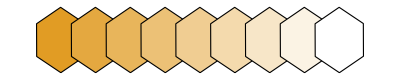

```mathematica
Graphics[Table[{Blend[{cols⟦1⟧,White},x],EdgeForm[{Black,Thin}],RegularPolygon[{8x,0},{0.8,11},6]},{x,0,1,1/8}]]
```

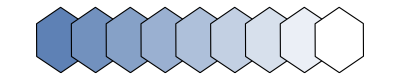

```mathematica
Graphics[Table[{Blend[{cols⟦2⟧,White},x],EdgeForm[{Black,Thin}],RegularPolygon[{8x,0},{0.8,11},6]},{x,0,1,1/8}]]
```

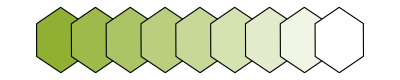

```mathematica
Graphics[Table[{Blend[{cols⟦3⟧,White},x],EdgeForm[{Black,Thin}],RegularPolygon[{8x,0},{0.8,11},6]},{x,0,1,1/8}]]
```